```mathematica
"Passo a passo de tudo até agora";
"Primeiramente Importar dados e nomear :";
"Para Importar : Insert->FilePath->...";
data = Import["C:\\Users\\Leoleo\\Desktop\\TCC\\Mathematica\\Interpolation\\116.dat"];
```

```mathematica
"Juntar Raio e Velocidades em Tabelas";
"Verificar Dimenções com -> Dimensions[data]";
 "data[[i,1]] -> Dados i da coluna 1";
RCtotal = Table[{data[[i,1]],data[[i,3]]},{i,1,15}];

RCgas = Table[{data[[i,1]],data[[i,4]]},{i,1,15}];
```

```mathematica
Erro = Table[data[[i,5]],{i,1,15}];
```

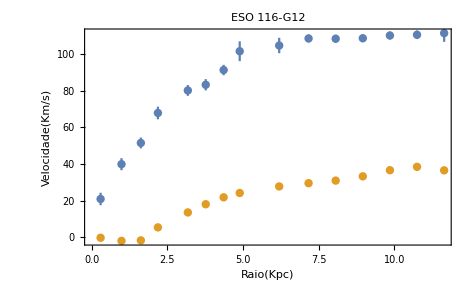

```mathematica
Needs["ErrorBarPlots`"];
 "Chama o pacote de erros";
"Prestar atenção nos indices, Todos os pares de dados tem que ter um erro nem que for 0";

RC =ErrorListPlot[{Table[{RCtotal[[i]],ErrorBar[Erro[[i]]]},{i,15}],Table[{RCgas[[i]],ErrorBar[0]},{i,15}]},Frame->True,PlotLabel->"ESO 116-G12",FrameLabel->{"Raio(Kpc)","Velocidade(Km/s)"}]
```

```mathematica
f = Interpolation[RCtotal];
```

```mathematica
g = Interpolation[RCgas];
```

```mathematica
Plot[f[x],{x,1,15}];
 "Mostra o grafíco da Interpolação";
```

```mathematica
a= Plot[{f[x],g[x]},{x,0.3,11.7},AxesOrigin->{x=0,x=0}];
```

```mathematica
"Coloquei até 12 pois até 15 fica ruim, o valor minimo de x é 0.3 pois é referente ao primeiro ponto";
```

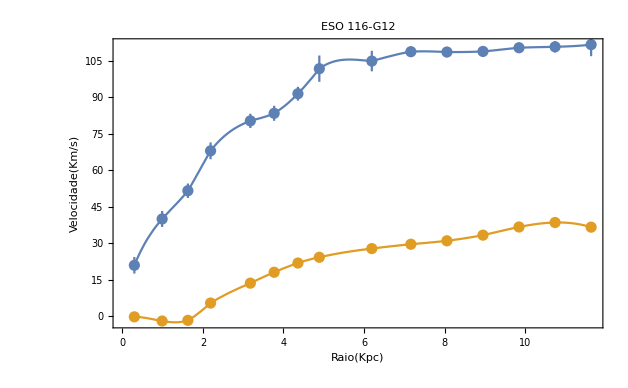

```mathematica
Final = Show[a,RC,Frame->True,FrameMargins->Small,FrameLabel->{"Raio(Kpc)","Velocidade(Km/s)"},PlotLabel->"ESO 116-G12"]
```